# 曲线的曲率

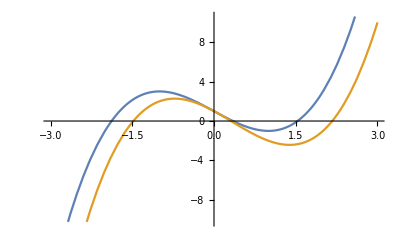

```mathematica
Plot[{x^3-3x+1,x^3-x^2-3x+1},{x,-3,3}]
```

```mathematica
f[x_]:=x^3/3-x+1
Manipulate[Show[Plot[{f[x]},{x,-3,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1],Graphics[{CircleThrough[Table[{x,f[x]},{x,{x0-d,x0,x0+d}}]],PointSize[Large],Magenta,Point[{x0,f[x0]}]}]],{{x0,1},-3,3},{d,0.1,0.2}]
```

CircleThrough::indep: {{-0.1,1.09967},{0.,1.},{0.1,0.900333}} 的 CircleThrough 不存在.

### 三角形与外接圆的关系

R=abc/(4S)